Condiciones iniciales: 547

Condiciones iniciales: 547

Puntos de Poincaré: 126195

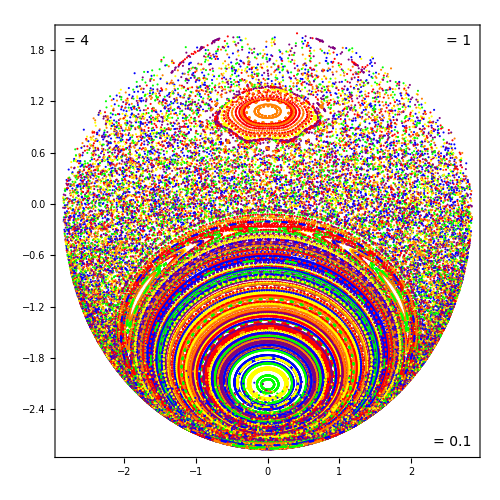

```mathematica
(*1. Parámetros*)
mu=1;
gamma=0.1;
Et=4;

(*2. Región de condiciones iniciales*)
xmax=Sqrt[2 (Et+mu gamma)];
vmax=xmax;
dx=0.2;
dv=0.2;
xmin=-xmax;
vmin=-vmax;

(*3. Energía del sistema*)
En[th_,x_,w_,v_]:=1/2 (1+mu) v^2+mu v w Cos[th]+1/2 mu w^2+1/2 x^2-mu gamma Cos[th];

(*4. Velocidad angular desde la energía*)
rad[x_,v_]:=(2 (Et+mu gamma)-x^2-v^2)/mu;
Omega[x_?NumericQ,v_?NumericQ]:=Module[{ww},If[rad[x,v]<0,Return[Missing["NoSolution"]]];
ww=-v+Sqrt[rad[x,v]];
If[ww>0,ww,Missing["NoSolution"]]];

(*5. Rejilla de condiciones iniciales*)
CI=DeleteMissing[Flatten[Table[Module[{w0=Omega[x0,v0]},If[NumericQ[w0],{x0,v0,w0},Missing["NoSolution"]]],{x0,xmin,xmax,dx},{v0,vmin,vmax,dv}],1]];

Print["Condiciones iniciales: ",Length[CI]];

(*6. Ecuaciones del Spring-Cart-Pendulum*)
SCPeqns={x'[t]==v[t],th'[t]==w[t],v'[t]==(mu w[t]^2 Sin[th[t]]+mu gamma Sin[th[t]] Cos[th[t]]-x[t])/(1+mu Sin[th[t]]^2),w'[t]==(x[t] Cos[th[t]]-mu w[t]^2 Sin[th[t]] Cos[th[t]]-(1+mu) gamma Sin[th[t]])/(1+mu Sin[th[t]]^2)};

(*7. Integración y sección de Poincaré*)
Tmax=1000;
datosPoincare=Table[Module[{x0,v0,w0,sol,puntos},{x0,v0,w0}=ci;
sol=Reap[NDSolve[Join[SCPeqns,{x[0]==x0,th[0]==0,v[0]==v0,w[0]==w0,WhenEvent[Sin[th[t]/2]==0,If[t>10^-8&&w[t]>0,Sow[{x[t],v[t]}]]]}],{x,th,v,w},{t,0,Tmax},MaxStepSize->0.01,MaxSteps->Infinity,AccuracyGoal->11,PrecisionGoal->11]];
puntos=If[Length[sol[[2]]]>0,sol[[2,1]],{}];
puntos],{ci,CI}];

Print["Condiciones iniciales: ",Length[CI]];
Print["Puntos de Poincaré: ",Total[Length/@datosPoincare]];

(*8. Colores por condición inicial*)
colores={Red,Orange,Yellow,Green,Blue,Purple};
estilos=Table[Directive[colores[[Mod[i-1,Length[colores]]+1]],PointSize[0.003]],{i,Length[datosPoincare]}];

(*9. Gráfica*)
ListPlot[datosPoincare,PlotStyle->estilos,Frame->True,Axes->False,PlotRange->All,AspectRatio->1,ImageSize->500,FrameLabel->{Style["",16],Style["",16]},LabelStyle->14,Epilog->{Inset[Style[Row[{" = ",mu}],14],Scaled[{0.98,0.98}],{Right,Top}],Inset[Style[Row[{" = ",Et}],14],Scaled[{0.02,0.98}],{Left,Top}],Inset[Style[Row[{" = ",gamma}],14],Scaled[{0.98,0.02}],{Right,Bottom}]}]
```

```mathematica
ListPlot[datosPoincare,PlotStyle->estilos,Frame->True,Axes->False,PlotRange->All,AspectRatio->1,ImageSize->500,FrameLabel->{Style["",16],Style["",16]},LabelStyle->14,Epilog->{Inset[Style[Row[{" = ",mu}],14],Scaled[{0.98,0.98}],{Right,Top}],Inset[Style[Row[{" = ",Et}],14],Scaled[{0.02,0.98}],{Left,Top}],Inset[Style[Row[{" = ",gamma}],14],Scaled[{0.98,0.02}],{Right,Bottom}]}]
```

-Graphics-